```mathematica
τ =1;
α =1;
β =2;
ΛH =1;
γc =1;
v =0.0001;
μc =0.000011;
μa =0.000001;
Λv =0.00000001;
μv =1;
```

```mathematica
DSolve[{IC'[t]== ΛH-β*Exp[-((τ^2*(IC[t]+IA[t])^2)/(α^2+(IC[t]+IA[t])^2))]*IV[t]+γc*IC[t]-(v+μc)*SC[t],IA'[t]==β*Exp[-((τ^2*(IC[t]+IA[t])^2)/(α^2+(IC[t]+IA[t])^2))]*IV[t]-(γc+μc)*IC[t], IV'[t]== v*SC[t]-β*Exp[-((τ^2*(IC[t]+IA[t])^2)/(α^2+(IC[t]+IA[t])^2))]*IV[t]+γa*IA[t]-μa*SA[t],SC'[t]== β*Exp[-((τ^2*(IC[t]+IA[t])^2)/(α^2+(IC[t]+IA[t])^2))]*IV[t]-(γa+μa)*IA[t], SA'[t]== Λv-μv*SV[t]-β*β*Exp[-((τ^2*(IC[t]+IA[t])^2)/(α^2+(IC[t]+IA[t])^2))]*IC[t]/SC[t]*SV[t] -β*β*Exp[-((τ^2*(IC[t]+IA[t])^2)/(α^2+(IC[t]+IA[t])^2))]*IA[t]/SA[t]*SV[t],  SV'[t]==  β*β*Exp[-((τ^2*(IC[t]+IA[t])^2)/(α^2+(IC[t]+IA[t])^2))]*IC[t]/SC[t]*SV[t]+ β*β*Exp[-((τ^2*(IC[t]+IA[t])^2)/(α^2+(IC[t]+IA[t])^2))]*IA[t]/SA[t]*SV[t]-μv*IV[t]},{IC[t],IA[t],IV[t],SC[t],SA[t],SV'[t]},t]
```

DSolve[{IC'[t]==1+IC[t]-2 ⅇ^(-(IA[t]+IC[t])^2/(1+(IA[t]+IC[t])^2)) IV[t]-0.000111 SC[t],IA'[t]==-1.00001 IC[t]+2 ⅇ^(-(IA[t]+IC[t])^2/(1+(IA[t]+IC[t])^2)) IV[t],IV'[t]==γa IA[t]-2 ⅇ^(-(IA[t]+IC[t])^2/(1+(IA[t]+IC[t])^2)) IV[t]-1.×10^-6 SA[t]+0.0001 SC[t],SC'[t]==-(1.×10^-6+γa) IA[t]+2 ⅇ^(-(IA[t]+IC[t])^2/(1+(IA[t]+IC[t])^2)) IV[t],SA'[t]==1.×10^-8-SV[t]-(4 ⅇ^(-(IA[t]+IC[t])^2/(1+(IA[t]+IC[t])^2)) IA[t] SV[t])/SA[t]-(4 ⅇ^(-(IA[t]+IC[t])^2/(1+(IA[t]+IC[t])^2)) IC[t] SV[t])/SC[t],SV'[t]==-IV[t]+(4 ⅇ^(-(IA[t]+IC[t])^2/(1+(IA[t]+IC[t])^2)) IA[t] SV[t])/SA[t]+(4 ⅇ^(-(IA[t]+IC[t])^2/(1+(IA[t]+IC[t])^2)) IC[t] SV[t])/SC[t]},{IC[t],IA[t],IV[t],SC[t],SA[t],SV'[t]},t]

```mathematica
ClearAll
```

ClearAll

```mathematica
sol=DSolve[{IC'[t]==IC[t],IC[0]==0},IC[t],t]
sol1= DSolve[{IA'[t]==IA[t],IA[1]== 0.0101001},IA[t],t]
sol2= DSolve[{IV'[t]==IV[t],IV[0]==0.00001 },IV[t],t]
sol3= DSolve[{SC'[t]==SC[t],SC[0]==2 },SC[t],t]
sol4= DSolve[{SA'[t]==SA[t],SA[5]==0.0088881 },SA[t],t]
sol5= DSolve[{SV'[t]==SV[t],SV[0.001010101010101]==0.00000000000000000001 },SV[t],t]
```

{{IC[t]→0}}

{{IA[t]→0.00371562 ⅇ^t}}

{{IV[t]→0.00001 ⅇ^t}}

{{SC[t]→2 ⅇ^t}}

{{SA[t]→0.0000598875 ⅇ^t}}

{{SV[t]→9.9899×10^-21 ⅇ^t}}

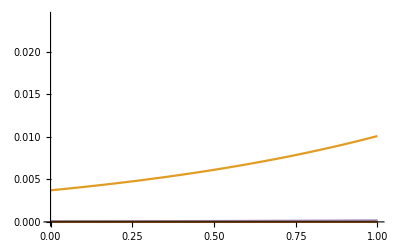

```mathematica
Plot[Evaluate[{IC[t]/.sol,IA[t]/.sol1, IV[t]/.sol2, SC[t]/.sol3,SA[t]/.sol4, SV[t]/.sol5}],{t,0,1}]
```